# Rosseler System: Poincare Sections-Forward Map

We store up all the Rosseler points were we cross a vertical plane

## Poincare Section: Forward Map.

We chose vertical plane through the lower equilibrium point.  We looked at two planes one containing the line y=x+b and the other containing y=-x+b.  Here is the one containing y=x+b with normal {1,-1,0}.

```mathematica
{a,b,c}={0.2,0.2,5.7};
center = {0.007026204834100129,-0.035131024170500645,0.035131024170500645};
{n1,n2}={{1,1,0},{1,-1,0}}; 
PlanePic= ContourPlot3D[ ({x,y,z}- center).n2 ==0, {x, -12,12},{y,-12,12},{z, 0, 20},
ContourStyle->Opacity[0.5]];
f[{x_,y_,z_}]:= {-y-z,x + a*y, b +z*(x-c)}
TMax=250;
StuffPlace={};
Quiet[
sol = NDSolveValue[{p'[t]==f[p[t]],p[0]=={0.2,0.4,13.4}},p,{t,0, TMax},
Method->{"EventLocator",
"Event":>((p[t]-center). n2),
"EventAction":>(StuffPlace={StuffPlace,p[t]}),
"Direction"->-1}];
]
Pic=ParametricPlot3D[sol[t],{t,0,TMax},
PlotPoints->200,
PlotRange->All,
PlotStyle->Thin];
StuffPlace=Partition[Flatten[StuffPlace],3];
m=Length[StuffPlace];
Show[Pic, 
PlanePic,
Graphics3D[Table[ {PointSize[0.02],Hue[i/(m+1)],Point[StuffPlace⟦i⟧]},{i, m}]],
AxesLabel->{"x","y","z"},
FaceGrids->All]
```

-Graphics3D-

We defined the forward map.

```mathematica
ForwardMap[p0_List]:=Module[{p,t,end},
Catch[
NDSolveValue[{p'[t]==f[p[t]],p[0]==p0},p,{t,0, 10^3},
Method->{"EventLocator",
"Event":>((p[t]-center). n2),
"EventAction":>Throw[end=p[t],"StopIntegration"],
"Direction"->-1}]; end]
]
```

We then saw that the forward map squashed the plane down onto what looke dlike a line but was actually just a thin stripe of a the section plane.  We plotted this on the plane so that it was easier to see.

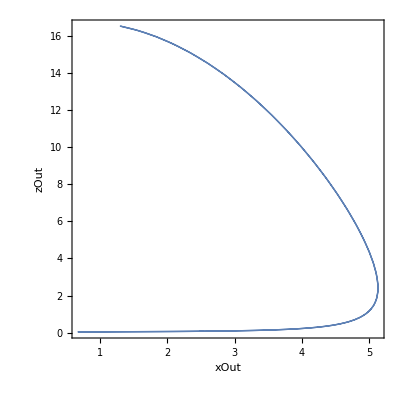

```mathematica
FPic=ParametricPlot[ ForwardMap[{x,x-0.042157229004600776,z}]⟦{1,3}⟧,
{x, 0.5,5},
{z,0,20},
PlotRange->All,
AspectRatio->1,
AxesLabel->{"xOut","zOut"}
]
```

If the Forward Map squishes things then the Backwards Map must expand things.  I am going to take a little patch around the curve (that is actually a sliver of a plane) and map it backwards.  I am going to do this near the bottom,

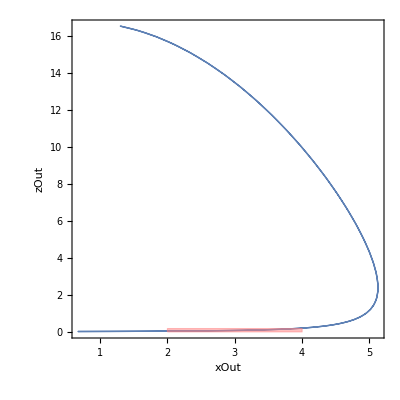

```mathematica
Show[FPic,Graphics[{Pink,Opacity[0.5],EdgeForm[Thin],Rectangle[{2,0.02},{4,0.2}]}]]
```

We get the backwards map by reversing time and reversing the “event” direction. If I do not change the “event” direction I only go half way. In other words to the “other side” of the plane. The problem is how fast the backwards ODE goes to pieces.

```mathematica
BackwardMap[p0_List]:=Module[{p,t,end},
Catch[
NDSolveValue[{p'[t]==-f[p[t]],p[0]==p0},p,{t,0, 10^3},
Method->{"EventLocator",Method->"ImplicitRungeKutta",
"Event":>((p[t]-center). n2),
"EventAction":>Throw[end=p[t],"StopIntegration"],
"Direction"->-1}]; end]
]
```

The tiny pink rectangle gets mapped backwards to

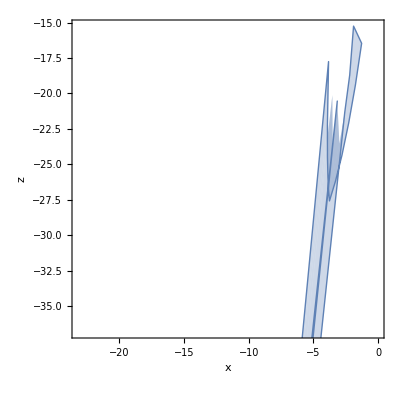

```mathematica
BPic=ParametricPlot[ BackwardMap[{x,x-0.042157229004600776,z}]⟦{1,3}⟧,
{x, 2,4},
{z,0.02,0.2},
(*PlotRange->All,*)
AspectRatio->1,
PlotPoints->6,
MaxRecursion->0,
AxesLabel->{"x","z"}
]
```

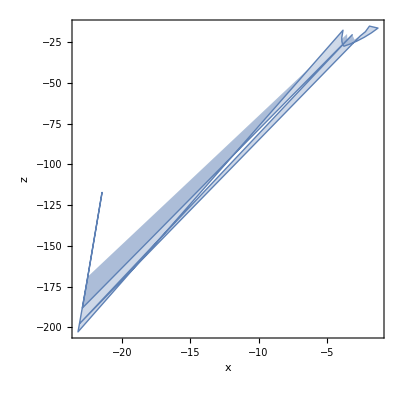

```mathematica
Show[BPic, PlotRange->All]
```

We are going to try to understand this using eigenvalues and a simpler function!